## Epicycloid (3:1)

Definition

```mathematica
f[t_]:=4/3 Cos[t]-1/3 Cos[4t]
```

```mathematica
g[t_]:=4/3 Sin[t]-1/3 Sin[4t]
```

FIgure

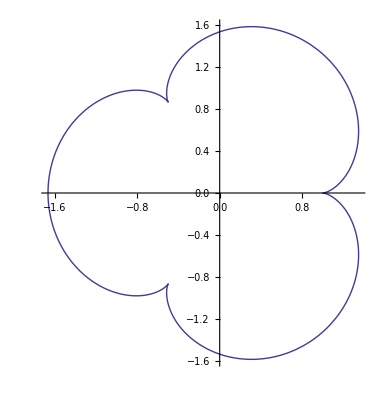

```mathematica
ParametricPlot[{f[t],g[t]},{t,0,2π}]
```

Area

```mathematica
df[t]=D[f[t],t]
```

-(4 Sin[t])/3+4/3 Sin[4 t]

```mathematica
S1=∫_(2/3 π)^0 g[t] df[t] ⅆt
```

(√3)/8+(20 π)/27

```mathematica
S2=1/2×3/2×(√3)/2
```

(3 √3)/8

```mathematica
S3=S1-S2
```

-(√3)/4+(20 π)/27

```mathematica
S=Simplify[3 S3 + 2 S2]
```

(20 π)/9